-Graphics3D-

-Graphics3D-

{6000.,8000.,2.,8.}

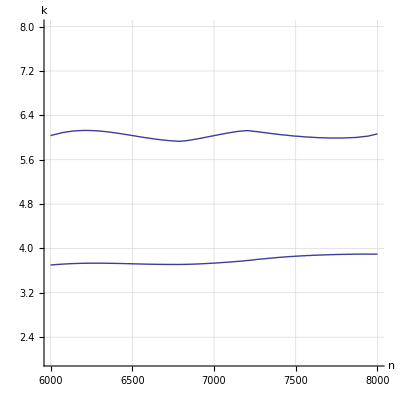

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
fname:="benchfile_6000-8000n_2-8k_2cores"
data:=Import[fname<>".txt", "CSV"]
par:=data[[All, {1,2,4}]]
seq:=data[[All, {1,2,3}]]
ppar =ListPlot3D[par,InterpolationOrder->1,Mesh->None,ColorFunction->Function[{x,y,z},Hue[z]],PlotRange->All,AxesLabel->{"n","k"},PlotLabel->"solver runtime"]
pseq=ListPlot3D[seq,InterpolationOrder->1,Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[z,z,z]],PlotRange->All,AxesLabel->{"n","k"},PlotLabel->"solver runtime"]
{nmin,nmax,kmin,kmax}={Min[par[[All,1]]]*1.0,Max[par[[All,1]]]*1.0,Min[par[[All,2]]]*1.0,Max[par[[All,2]]]*1.0}
cplot=ContourPlot[Interpolation[par][x,y]==Interpolation[seq][x,y]//Evaluate,{x,nmin,nmax},{y,kmin,kmax},Axes->True,Frame->False,AxesLabel->{"n","k"},PerformanceGoal->Quality, PlotRangeClipping->True,PlotRange->{{6000,nmax}, {2,kmax}},GridLines->Automatic]
parseq:=Show[ppar,pseq,Axes->True,PlotLabel->"Solver Runtime",AxesLabel->{"n","k"}]
parseq
Export[fname<>"-par.pdf",ppar];
Export[fname<>"-seq.pdf",pseq];
Export[fname<>"-parseq.pdf",parseq];
Export[fname<>"-contour.pdf",cplot];
```